## Distribution Experiements

### Normal Distribution

```mathematica
Clear[ν];νrange = {15, 18}; normDist := NormalDistribution[ν,1];
```

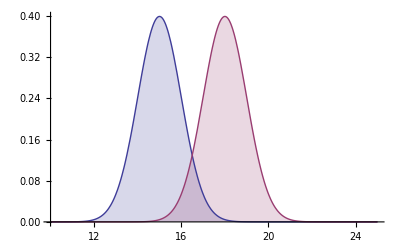

```mathematica
Plot[Evaluate@Table[PDF[normDist,x],{ν,νrange}], {x,10,25},Filling-> Axis]
```

```mathematica
dataNormDist = Table[RandomVariate[normDist,1000],{ν,νrange}]
```

(14.3213 | 14.4016 | 15.7758 | 15.8397 | 14.404 | 14.345 | 16.5277 | 15.2107 | 13.5973 | 15.8586 | 15.7076 | 13.7925 | 14.1447 | 15.1029 | 14.6095 | 12.8105 | 15.1167 | 13.9481 | 14.4184 | 15.7251 | 14.8838 | 15.2095 | 14.4592 | 14.8757 | 14.8511 | 15.7182 | 13.8792 | 14.286 | 14.7722 | 13.4612 | 15.6549 | 15.3255 | 13.3652 | 14.7625 | 15.3898 | 13.0575 | 15.6903 | 14.6559 | 14.4366 | 15.2189 | 14.9768 | 15.4034 | 15.079 | 15.2675 | 15.4029 | 13.3245 | 13.4203 | 14.6427 | 16.8084 | 16.2537 | 15.7312 | 14.1363 | 14.2463 | 15.4051 | 16.0134 | 15.3932 | 15.1376 | 15.6817 | 16.2556 | 16.0099 | 14.3991 | 14.6719 | 15.9309 | 14.5882 | 15.5377 | 13.2563 | 14.7507 | 16.406 | 15.1407 | 15.4985 | 14.0695 | 14.9974 | 16.7475 | 14.8263 | 15.7359 | 14.9162 | 15.1416 | 14.6119 | 14.0146 | 15.4843 | 15.0085 | 17.0635 | 14.6909 | 15.1719 | 16.1589 | 16.4721 | 14.1962 | 14.7406 | 12.2127 | 14.1497 | 15.0493 | 15.5439 | 13.4956 | 15.1368 | 15.1916 | 16.3705 | 16.3386 | 15.2668 | 18.7444 | 13.2379 | 15.085 | 13.4668 | 15.3808 | 14.7183 | 13.9504 | 14.5333 | 15.6189 | 14.9295 | 14.7979 | 13.0769 | 16.1979 | 16.0453 | 15.9266 | 15.8808 | 15.071 | 14.9278 | 15.8576 | 14.3643 | 15.9989 | 14.6922 | 15.2616 | 14.5491 | 13.4278 | 15.9283 | 15.4497 | 15.8532 | 14.0023 | 15.2433 | 13.734 | 14.1342 | 13.238 | 15.4948 | 14.8625 | 14.8638 | 15.2832 | 16.1273 | 13.908 | 14.9676 | 14.4501 | 14.879 | 14.3072 | 14.0237 | 14.554 | 14.2695 | 14.5189 | 16.3719 | 15.2464 | 13.755 | 15.3299 | 16.8456 | 15.849 | 16.9251 | 13.3689 | 14.7133 | 16.7305 | 14.595 | 14.9091 | 14.2468 | 13.8109 | 16.0671 | 16.1836 | 14.7277 | 15.943 | 14.1901 | 15.9273 | 14.1543 | 14.5418 | 15.1089 | 15.254 | 15.6059 | 14.5047 | 14.8648 | 16.5345 | 14.1139 | 16.8829 | 16.295 | 14.0631 | 14.8057 | 15.6605 | 15.2661 | 15.6018 | 15.2643 | 14.5015 | 17.136 | 16.9029 | 15.6271 | 15.4145 | 17.9247 | 15.8301 | 15.9571 | 14.4664 | 15.5588 | 14.2944 | 13.7561 | 15.2303 | 14.6579 | 15.7532 | 15.7202 | 15.1137 | 14.616 | 14.8782 | 14.0034 | 14.6498 | 16.3384 | 13.9962 | 15.3782 | 14.0739 | 14.999 | 16.628 | 14.0913 | 13.4065 | 14.2167 | 12.0088 | 15.5817 | 14.8686 | 15.0007 | 16.7406 | 15.1576 | 14.3635 | 15.3908 | 16.1755 | 15.6675 | 14.0375 | 14.7743 | 14.017 | 15.2937 | 16.725 | 15.3655 | 13.3381 | 14.5176 | 16.1883 | 15.0707 | 15.7079 | 13.5673 | 15.9115 | 15.967 | 14.0572 | 15.2718 | 14.029 | 14.998 | 15.997 | 15.3702 | 16.0294 | 15.8143 | 14.1671 | 15.0308 | 15.18 | 14.2485 | 14.2568 | 14.3302 | 14.421 | 15.262 | 14.243 | 14.0847 | 15.1223 | 14.9099 | 12.9869 | 15.3313 | 16.2144 | 15.6568 | 13.7866 | 13.9262 | 16.0978 | 16.3751 | 15.1698 | 13.8899 | 15.5991 | 13.5898 | 14.2246 | 15.053 | 14.4367 | 12.9793 | 14.6488 | 16.3135 | 15.1787 | 15.6392 | 16.618 | 14.2799 | 15.6669 | 15.3164 | 14.7631 | 15.3149 | 14.673 | 14.4317 | 17.2182 | 16.7573 | 15.7271 | 15.1265 | 17.0039 | 15.8438 | 15.0642 | 14.8097 | 15.9285 | 13.9024 | 14.4034 | 15.7247 | 14.6737 | 15.3433 | 14.9995 | 14.7081 | 16.1141 | 15.0141 | 15.0244 | 15.2767 | 15.7815 | 14.4872 | 15.0151 | 16.8706 | 15.5698 | 14.0343 | 13.8744 | 15.859 | 15.691 | 16.3743 | 14.1025 | 15.8028 | 15.6096 | 15.7669 | 15.8557 | 15.3184 | 15.0692 | 15.1753 | 14.4019 | 14.7824 | 14.4955 | 13.5872 | 15.8166 | 15.1614 | 15.1154 | 14.1184 | 13.6052 | 14.4224 | 15.5533 | 14.9341 | 15.1128 | 14.3069 | 15.2558 | 14.2168 | 16.9784 | 13.9727 | 14.5317 | 14.9577 | 14.4043 | 15.2335 | 14.163 | 15.8247 | 16.1287 | 14.8618 | 13.2063 | 16.995 | 14.6318 | 14.8019 | 15.4022 | 14.7175 | 14.7827 | 14.406 | 14.1486 | 15.102 | 15.1993 | 15.2936 | 15.1131 | 15.2791 | 15.7512 | 13.9147 | 16.9447 | 14.6791 | 15.1477 | 15.6619 | 16.0167 | 13.9523 | 16.128 | 14.3412 | 16.3696 | 17.6913 | 15.9869 | 15.5558 | 15.0138 | 15.5151 | 13.9235 | 15.0374 | 15.4607 | 14.6684 | 15.3275 | 15.8252 | 15.9387 | 15.5291 | 13.8854 | 15.1676 | 15.2915 | 14.675 | 15.4382 | 14.5136 | 16.5301 | 15.5908 | 14.5638 | 14.1655 | 15.0122 | 16.4383 | 15.0965 | 15.5801 | 14.2093 | 16.0167 | 13.8074 | 15.3349 | 13.4739 | 14.9159 | 14.7918 | 15.3535 | 12.856 | 15.0763 | 15.239 | 15.6243 | 16.5379 | 14.2739 | 14.2334 | 14.2918 | 15.0115 | 15.6253 | 14.9433 | 14.0134 | 14.6675 | 13.9229 | 14.8079 | 14.4554 | 14.153 | 15.4877 | 16.8063 | 15.8661 | 15.6277 | 12.9596 | 14.3132 | 17.0107 | 13.9726 | 14.4534 | 15.5089 | 14.368 | 15.1132 | 14.7665 | 14.8712 | 14.7571 | 13.9846 | 14.7918 | 14.853 | 14.1388 | 14.0229 | 13.1891 | 15.4168 | 14.6435 | 15.6101 | 13.9803 | 14.4516 | 15.246 | 15.4529 | 15.4199 | 14.3523 | 14.7792 | 15.7236 | 14.4488 | 13.5629 | 16.1485 | 15.0336 | 15.2441 | 15.3261 | 15.0355 | 14.7096 | 14.4589 | 15.452 | 16.9462 | 14.6744 | 15.2485 | 15.2346 | 17.0029 | 15.735 | 15.468 | 15.4766 | 14.3241 | 14.7562 | 15.6721 | 17.2102 | 14.9696 | 16.4611 | 14.7236 | 16.1382 | 14.8024 | 14.7744 | 13.8164 | 13.4987 | 13.1369 | 15.3554 | 13.1812 | 15.64 | 15.8191 | 16.2267 | 14.432 | 12.9308 | 14.1765 | 14.1164 | 15.7517 | 15.3359 | 13.8414 | 14.3278 | 14.7918 | 16.9089 | 16.9626 | 15.2733 | 14.9341 | 14.5048 | 13.04 | 15.2793 | 14.98 | 14.425 | 14.0611 | 14.0769 | 14.8252 | 14.2918 | 14.4634 | 15.3443 | 15.9547 | 15.9735 | 16.7924 | 16.1831 | 16.0832 | 15.8408 | 15.5691 | 15.1379 | 14.2486 | 15.4294 | 14.2402 | 14.4162 | 14.0437 | 14.9386 | 14.2567 | 15.2237 | 15.2568 | 16.1137 | 15.5822 | 15.4329 | 14.497 | 16.3436 | 14.7141 | 13.852 | 15.3528 | 16.3367 | 15.0328 | 16.3902 | 14.4818 | 14.9259 | 17.4443 | 15.0027 | 16.2875 | 16.0374 | 15.9409 | 15.5049 | 14.1226 | 14.5177 | 13.5121 | 13.4852 | 17.0021 | 14.843 | 15.764 | 15.3186 | 16.7887 | 14.7812 | 14.716 | 14.1436 | 16.2681 | 13.7296 | 15.5379 | 15.5446 | 14.8314 | 15.2754 | 15.9955 | 15.5468 | 13.6955 | 15.6344 | 17.0435 | 14.2085 | 15.7117 | 14.0959 | 13.2553 | 13.9289 | 12.6952 | 15.1115 | 14.558 | 15.4499 | 16.2579 | 15.75 | 14.6084 | 13.7409 | 15.6832 | 14.5532 | 15.886 | 13.1417 | 14.2766 | 14.2948 | 16.7024 | 14.1935 | 15.8343 | 14.0081 | 15.2654 | 15.7347 | 14.683 | 15.3645 | 16.0264 | 13.3695 | 15.1768 | 13.921 | 16.3194 | 15.6757 | 15.7985 | 16.2137 | 15.3229 | 16.0877 | 14.8621 | 15.8017 | 15.3216 | 13.8649 | 14.8548 | 15.5354 | 14.3867 | 14.6548 | 14.2205 | 16.3911 | 15.5827 | 15.3796 | 12.7785 | 15.6503 | 14.7768 | 14.1506 | 14.9302 | 15.7056 | 13.8895 | 14.1906 | 15.1686 | 14.9595 | 15.7319 | 14.3295 | 16.2081 | 16.4273 | 13.8722 | 12.5214 | 14.5895 | 13.5929 | 14.0496 | 15.1882 | 15.1856 | 14.1609 | 14.8775 | 14.4663 | 15.4224 | 12.8016 | 14.5864 | 16.2442 | 14.5346 | 14.3222 | 14.663 | 12.8386 | 14.9615 | 13.7082 | 14.647 | 15.093 | 15.2893 | 14.9074 | 13.7055 | 16.5858 | 16.3275 | 17.3125 | 16.5623 | 14.4671 | 14.7788 | 15.6751 | 13.5814 | 15.5906 | 15.0808 | 15.608 | 15.1174 | 13.5746 | 15.0328 | 16.9417 | 14.6594 | 14.5223 | 16.4752 | 15.9629 | 15.0388 | 16.3241 | 15.6951 | 15.5077 | 17.1222 | 15.7945 | 15.8046 | 16.1288 | 14.7743 | 14.4525 | 13.9066 | 14.9276 | 16.7556 | 14.8424 | 14.4235 | 15.1669 | 14.3255 | 16.9567 | 15.8256 | 14.0787 | 17.3106 | 15.1875 | 14.1579 | 13.4601 | 14.9778 | 13.7404 | 15.1526 | 13.7926 | 14.1951 | 15.8606 | 15.0318 | 13.9276 | 15.3483 | 15.3955 | 15.6189 | 15.4038 | 15.1649 | 15.7283 | 14.9655 | 14.8734 | 15.9448 | 15.2175 | 15.6472 | 14.8111 | 16.4318 | 15.0757 | 16.5156 | 13.6525 | 16.5929 | 16.1395 | 16.6901 | 14.5873 | 15.6473 | 13.2579 | 15.3183 | 16.5907 | 15.0706 | 14.6465 | 15.1392 | 13.9876 | 14.9759 | 15.1178 | 16.3259 | 14.8263 | 17.2237 | 14.9055 | 15.4664 | 15.7159 | 16.4798 | 13.6659 | 14.4693 | 15.0371 | 15.1333 | 16.0184 | 14.017 | 14.0153 | 14.4136 | 14.6797 | 14.016 | 13.3128 | 15.2103 | 15.2411 | 15.7986 | 14.4766 | 14.4032 | 14.3848 | 15.0401 | 15.6681 | 15.7952 | 15.3651 | 14.8416 | 16.2444 | 12.8837 | 14.9965 | 14.3628 | 14.2622 | 14.32 | 17.2417 | 14.7589 | 15.3275 | 15.7151 | 13.5182 | 15.1944 | 14.8653 | 15.4149 | 15.8873 | 13.6156 | 15.5554 | 15.9182 | 15.529 | 13.326 | 15.2192 | 15.0366 | 13.9766 | 14.9647 | 15.0585 | 15.2293 | 14.1213 | 15.5599 | 14.4709 | 14.2623 | 15.4175 | 16.6534 | 14.6688 | 16.1611 | 14.8098 | 14.2161 | 15.5353 | 14.5182 | 14.4541 | 15.9198 | 17.2818 | 14.0129 | 13.2016 | 13.1127 | 15.9063 | 15.4182 | 15.3356 | 14.2539 | 16.3378 | 13.7759 | 13.9739 | 15.1635 | 14.3768 | 14.4335 | 14.6593 | 14.8507 | 14.8706 | 14.7393 | 14.6717 | 15.9181 | 15.1834 | 15.0925 | 13.3055 | 13.7868 | 15.2772 | 13.7553 | 14.5401 | 15.0107 | 14.3284 | 16.176 | 14.4602 | 15.5998 | 14.8736 | 14.8937 | 15.435 | 14.5941 | 15.5346 | 15.3877 | 13.4457 | 15.1819 | 14.5803 | 16.1588 | 15.7498 | 15.4862 | 14.4216 | 16.5697 | 14.7098 | 14.4065 | 15.4636 | 14.4843 | 13.8932 | 14.9307 | 14.8858 | 16.0189 | 15.6713 | 13.8308 | 15.1015 | 15.4232 | 13.73 | 13.4166 | 15.44 | 13.58 | 15.8732 | 17.2219 | 14.9216 | 15.3569 | 13.7026 | 14.7873 | 15.2667 | 14.5018 | 13.9049 | 13.9017 | 14.3633 | 16.326 | 14.676 | 13.8805 | 14.5592 | 15.5016 | 15.5093 | 15.3966 | 15.0231 | 14.8449 | 15.6606 | 16.2045 | 13.0991 | 15.0806 | 14.6852 | 15.1053 | 14.4891 | 16.5139 | 13.4052 | 15.7833 | 13.5351 | 13.5018 | 16.0967 | 15.2038 | 17.6673 | 14.055 | 14.797 | 15.002 | 14.2943 | 16.5241 | 13.865 | 15.3289 | 15.2764 | 14.226 | 16.1474 | 14.6074 | 12.8626 | 14.0258 | 15.9585 | 13.4185 | 15.322 | 15.8771 | 15.8762 | 15.3348 | 13.9594 | 15.4017 | 16.2295 | 16.0707 | 15.5151 | 16.686 | 14.5574 | 17.2004 | 14.772 | 14.6378 | 14.6694 | 15.9454 | 16.0608 | 14.884 | 14.6785 | 16.4305 | 13.9741 | 17.1087 | 16.7753 | 13.3552 | 14.5717 | 14.1551 | 13.9898 | 15.342 | 14.353 | 13.765 | 14.8817 | 15.3873 | 15.2702 | 13.4805 | 13.8136 | 14.6326 | 14.4133 | 14.8441 | 13.1482 | 14.0752 | 15.3645 | 13.0441 | 12.3144 | 14.7746 | 14.86 | 14.9887 | 12.9037 | 14.4294 | 14.9536 | 15.1373 | 16.1845 | 14.5876 | 16.115 | 14.4827 | 16.4504 | 15.1211 | 14.2376 | 15.3954 | 14.7577 | 15.2556 | 13.5528 | 15.1519 | 14.4634 | 15.9203 | 13.9862 | 12.052 | 13.6777 | 14.4483 | 14.9428 | 15.0455 | 14.7774 | 16.5718 | 13.4755 | 13.3337
17.989 | 17.4913 | 16.7518 | 18.5588 | 17.7255 | 18.304 | 19.4616 | 17.7707 | 16.6244 | 19.3152 | 18.3221 | 18.5321 | 18.2385 | 18.5929 | 18.4194 | 16.9161 | 16.663 | 16.4956 | 18.4929 | 17.374 | 18.3087 | 18.1622 | 19.2161 | 17.0827 | 18.0344 | 17.7991 | 18.2246 | 19.3709 | 17.6488 | 18.2431 | 17.0996 | 17.2722 | 18.6256 | 18.6632 | 18.209 | 17.9739 | 18.5869 | 16.3422 | 18.7461 | 18.8306 | 18.868 | 16.7537 | 16.6161 | 17.4926 | 15.3098 | 17.5466 | 17.9744 | 20.0024 | 17.8701 | 18.8512 | 17.7157 | 20.6054 | 16.922 | 18.1975 | 17.5022 | 18.2603 | 19.0413 | 18.4521 | 18.2665 | 19.5764 | 19.0389 | 18.9048 | 17.0501 | 18.4035 | 17.9719 | 19.247 | 18.209 | 18.6139 | 18.7149 | 18.5736 | 18.8672 | 16.9432 | 15.9646 | 17.4211 | 18.8479 | 19.309 | 18.1249 | 17.6938 | 15.3047 | 16.7636 | 17.3971 | 17.3166 | 19.3477 | 18.7113 | 18.3488 | 18.8171 | 16.6236 | 15.9167 | 18.935 | 18.2175 | 18.3987 | 19.1616 | 15.1334 | 17.4805 | 16.9292 | 18.4637 | 18.96 | 19.995 | 17.6602 | 19.7877 | 19.5936 | 18.5954 | 18.1362 | 16.8971 | 18.4423 | 18.8338 | 17.7205 | 19.9911 | 17.982 | 18.006 | 18.9564 | 17.5059 | 18.4629 | 19.445 | 20.2491 | 15.6016 | 17.2198 | 16.9258 | 17.0083 | 16.6919 | 18.6197 | 17.7532 | 18.397 | 17.9565 | 18.4897 | 18.0457 | 17.7444 | 19.5443 | 18.7911 | 18.0467 | 17.2827 | 20.934 | 15.8508 | 17.704 | 16.6299 | 18.5599 | 17.3043 | 18.8493 | 15.9577 | 18.9799 | 15.9962 | 17.2306 | 17.0657 | 18.3661 | 20.1649 | 18.9457 | 17.8477 | 16.369 | 17.446 | 18.2048 | 16.9356 | 18.389 | 18.74 | 17.7692 | 15.6824 | 17.4439 | 19.6487 | 17.0053 | 17.6834 | 18.5314 | 18.6692 | 17.8958 | 18.2505 | 16.9054 | 18.9711 | 16.5125 | 16.7826 | 18.2792 | 18.4299 | 19.2407 | 19.7057 | 18.0168 | 18.4749 | 17.6087 | 18.0165 | 16.6322 | 18.7506 | 19.0844 | 18.4216 | 17.6849 | 15.903 | 16.0107 | 17.5752 | 18.374 | 17.2162 | 19.3826 | 18.652 | 16.8389 | 17.2166 | 17.076 | 16.8868 | 17.6477 | 16.5617 | 17.5691 | 19.2574 | 17.2288 | 17.7153 | 18.4315 | 17.7101 | 18.2319 | 18.4368 | 17.1353 | 17.0326 | 17.8953 | 18.0548 | 16.9733 | 18.6566 | 17.8638 | 17.8237 | 18.5749 | 17.5072 | 18.0974 | 14.9296 | 18.7208 | 20.4677 | 17.857 | 19.3915 | 17.4133 | 17.7699 | 16.9985 | 17.6407 | 17.2931 | 16.1285 | 17.3507 | 17.3406 | 16.0132 | 17.6501 | 18.5588 | 18.5276 | 16.5875 | 19.7264 | 18.6194 | 18.1171 | 17.4095 | 19.2792 | 18.9934 | 17.1501 | 17.4363 | 19.9508 | 15.9436 | 18.9929 | 18.8663 | 17.6255 | 19.2883 | 18.1197 | 18.4256 | 18.4706 | 17.3822 | 16.6871 | 17.6102 | 16.6712 | 19.9475 | 16.9791 | 16.6119 | 17.7809 | 18.6126 | 20.1111 | 18.4942 | 17.862 | 19.8882 | 18.5204 | 17.8162 | 17.6338 | 17.9805 | 18.8232 | 17.7423 | 17.9699 | 16.4203 | 15.4916 | 19.1033 | 19.5409 | 16.781 | 18.9224 | 17.6115 | 15.5117 | 19.9576 | 16.4031 | 19.1536 | 19.683 | 18.1059 | 17.5953 | 19.0037 | 16.6804 | 17.5298 | 17.9098 | 17.9469 | 19.0578 | 17.4468 | 19.2485 | 16.5151 | 17.9239 | 16.0492 | 17.3211 | 18.2365 | 16.4036 | 19.1815 | 17.1795 | 17.6554 | 19.1704 | 18.23 | 16.8482 | 17.7955 | 18.2074 | 17.6432 | 17.4181 | 17.975 | 16.9355 | 17.6937 | 17.5658 | 18.8818 | 17.081 | 17.6922 | 16.5357 | 17.8537 | 18.963 | 17.351 | 17.2257 | 17.0861 | 18.3183 | 17.4061 | 17.8467 | 16.81 | 17.2719 | 16.6752 | 19.4375 | 18.6277 | 20.0948 | 16.5082 | 17.6374 | 19.5997 | 17.9492 | 19.2902 | 16.3068 | 16.4873 | 19.2943 | 18.9947 | 18.9783 | 18.023 | 17.8579 | 17.5201 | 16.4281 | 18.0187 | 17.7007 | 18.7312 | 17.9778 | 19.469 | 16.8957 | 17.5955 | 19.2857 | 18.3292 | 17.3866 | 17.3697 | 16.3495 | 16.8879 | 18.5197 | 19.5737 | 18.2181 | 17.5934 | 18.4734 | 17.4762 | 21.0706 | 19.7147 | 18.5302 | 17.2084 | 17.3701 | 20.9239 | 16.9501 | 18.9708 | 15.6665 | 17.7784 | 17.7429 | 17.5967 | 17.8452 | 19.639 | 18.2361 | 17.6822 | 17.318 | 16.9222 | 17.2962 | 18.179 | 18.8901 | 19.007 | 17.3171 | 17.6049 | 18.841 | 17.8015 | 18.5782 | 19.1868 | 17.4404 | 15.232 | 17.0477 | 17.3939 | 19.7908 | 17.3392 | 18.5352 | 19.1961 | 19.3438 | 17.6676 | 17.4542 | 19.1787 | 17.9597 | 19.9287 | 19.4976 | 18.5412 | 20.1516 | 16.7984 | 17.7975 | 17.906 | 16.2103 | 19.261 | 18.5515 | 18.4907 | 16.1251 | 17.3365 | 17.5603 | 18.682 | 19.8301 | 16.5879 | 18.0763 | 18.4709 | 18.1122 | 17.2166 | 17.9617 | 19.6563 | 16.9887 | 17.1986 | 18.6213 | 16.4787 | 17.6304 | 19.8839 | 18.5749 | 18.3044 | 20.1372 | 18.7164 | 18.6846 | 18.9609 | 18.0246 | 17.7268 | 15.9998 | 18.2103 | 16.4446 | 18.3256 | 17.5344 | 17.4618 | 17.4626 | 17.8693 | 18.4011 | 17.5188 | 16.3316 | 17.4243 | 20.3403 | 19.6322 | 17.4807 | 16.6767 | 18.9275 | 17.4294 | 18.9308 | 18.7198 | 17.5383 | 18.5876 | 19.3475 | 18.0346 | 17.1581 | 18.641 | 17.5779 | 17.2457 | 16.0245 | 17.2094 | 17.8231 | 17.2537 | 17.8444 | 18.5607 | 17.1131 | 17.9669 | 18.5282 | 18.4056 | 18.7135 | 16.685 | 17.9732 | 18.6327 | 18.1684 | 19.3151 | 20.1735 | 18.6034 | 19.6624 | 18.1341 | 17.1765 | 19.7191 | 17.8457 | 19.3129 | 18.1041 | 16.0713 | 17.9578 | 17.9864 | 18.9542 | 18.6809 | 19.7394 | 17.3293 | 16.9714 | 18.5328 | 18.841 | 17.3623 | 18.4818 | 17.6781 | 17.716 | 16.8511 | 17.544 | 17.3563 | 18.9004 | 20.1059 | 18.1753 | 16.6843 | 18.388 | 18.9635 | 18.869 | 18.6134 | 17.6683 | 17.9395 | 17.8177 | 19.0318 | 16.9103 | 16.9318 | 19.6002 | 19.1473 | 18.0069 | 17.8651 | 16.8931 | 18.472 | 17.8658 | 17.6231 | 17.1113 | 19.2837 | 16.4566 | 17.7977 | 17.2561 | 16.8672 | 17.6721 | 18.7224 | 17.4823 | 16.4771 | 16.6466 | 17.2888 | 17.2154 | 20.1545 | 17.2615 | 20.3068 | 18.3065 | 19.8078 | 19.5649 | 19.3522 | 17.9587 | 18.8773 | 19.0997 | 19.4377 | 17.6508 | 17.6431 | 17.4195 | 18.132 | 16.2761 | 17.8113 | 17.5813 | 18.2608 | 18.2329 | 17.8778 | 17.1364 | 17.618 | 17.2631 | 19.1366 | 17.4401 | 19.2832 | 16.5687 | 17.4006 | 17.1895 | 17.5286 | 18.7779 | 18.2267 | 18.5393 | 18.9837 | 19.1322 | 17.9058 | 18.0385 | 17.9651 | 18.1945 | 18.5036 | 18.1886 | 17.5292 | 18.8985 | 18.921 | 18.448 | 18.7624 | 17.1586 | 18.1266 | 17.2527 | 18.9482 | 18.7995 | 19.3703 | 17.721 | 17.6793 | 19.1431 | 17.2784 | 17.1069 | 18.1257 | 18.4363 | 17.0174 | 17.6244 | 17.1842 | 18.4611 | 17.4821 | 19.2982 | 18.6073 | 18.2315 | 18.104 | 18.0723 | 16.0853 | 17.9437 | 18.1939 | 17.8494 | 18.6605 | 17.7251 | 17.7916 | 18.4688 | 16.8567 | 18.4296 | 17.9519 | 18.8984 | 18.3785 | 17.4761 | 17.5037 | 17.5373 | 18.318 | 16.9963 | 17.2962 | 15.9479 | 17.7565 | 19.3714 | 17.6529 | 16.1798 | 18.1004 | 20.2602 | 17.6651 | 18.6785 | 17.6135 | 19.0607 | 17.8787 | 19.6028 | 16.5605 | 19.3613 | 17.5275 | 18.2197 | 17.8701 | 18.8185 | 15.9661 | 16.6221 | 15.8308 | 17.4057 | 17.2681 | 18.4388 | 17.0247 | 18.5467 | 18.015 | 17.9008 | 17.4873 | 19.3686 | 17.1225 | 16.9688 | 19.3985 | 18.7019 | 18.1999 | 17.8765 | 17.5228 | 16.1964 | 16.2068 | 18.288 | 16.4533 | 18.1499 | 19.2292 | 18.3563 | 18.8096 | 18.0676 | 17.7595 | 18.2172 | 18.7156 | 17.1934 | 20.1097 | 16.759 | 17.8809 | 19.2904 | 15.5369 | 19.2223 | 17.3242 | 16.6399 | 16.5072 | 16.7968 | 18.6296 | 18.0428 | 18.4363 | 18.9378 | 17.5927 | 16.9058 | 17.6095 | 17.9821 | 17.6112 | 16.6407 | 18.7909 | 17.9373 | 17.0246 | 16.9611 | 16.5715 | 18.0621 | 17.5729 | 19.1522 | 18.4023 | 17.5409 | 20.5204 | 18.2408 | 18.976 | 17.949 | 16.8839 | 17.2788 | 17.7591 | 17.9627 | 17.1386 | 18.3282 | 17.595 | 18.17 | 16.4708 | 17.9749 | 19.4207 | 19.6608 | 18.1846 | 18.6864 | 17.1589 | 19.2707 | 18.0523 | 18.3638 | 18.7514 | 17.0607 | 17.1123 | 18.4887 | 17.0165 | 17.1029 | 18.9077 | 18.1184 | 19.0283 | 19.9375 | 18.174 | 17.9767 | 18.6921 | 18.1873 | 17.6532 | 18.8097 | 19.416 | 19.3882 | 20.1772 | 18.5181 | 15.1549 | 17.952 | 18.7112 | 18.8091 | 19.2084 | 18.2951 | 18.5566 | 17.8561 | 16.9291 | 19.0293 | 17.6774 | 17.4864 | 18.0204 | 16.7092 | 17.8088 | 19.7648 | 19.0221 | 18.6448 | 16.7467 | 17.7918 | 18.2253 | 16.8711 | 18.2285 | 18.9882 | 19.2064 | 19.396 | 18.3022 | 17.9907 | 17.3785 | 19.6869 | 19.2027 | 17.6962 | 16.6219 | 17.0819 | 19.1759 | 18.5984 | 18.3098 | 16.9873 | 17.5402 | 17.9452 | 17.0286 | 18.1364 | 18.951 | 17.5736 | 17.8887 | 16.4111 | 16.8256 | 17.2894 | 16.7994 | 15.6926 | 17.4317 | 17.3149 | 17.7565 | 17.2685 | 17.8139 | 15.9947 | 17.7238 | 19.2049 | 17.5156 | 18.1473 | 19.2607 | 18.0798 | 19.0638 | 17.3852 | 18.8759 | 18.8396 | 19.6003 | 18.2754 | 18.1253 | 18.2153 | 18.6742 | 16.9308 | 17.2915 | 16.9994 | 17.4417 | 17.7005 | 17.8642 | 17.151 | 17.1119 | 16.1825 | 18.0225 | 16.4461 | 18.5853 | 17.3281 | 18.0366 | 17.6635 | 17.5949 | 17.696 | 18.559 | 18.5573 | 17.7234 | 16.5342 | 18.533 | 17.0474 | 15.4064 | 19.259 | 18.4389 | 16.1766 | 19.2076 | 17.5384 | 17.8309 | 18.2219 | 17.9449 | 17.9496 | 18.8474 | 17.6889 | 16.2246 | 18.66 | 17.258 | 19.2279 | 17.3081 | 17.6372 | 17.3609 | 19.715 | 18.7631 | 19.2835 | 18.5775 | 18.049 | 20.2065 | 18.7164 | 15.9857 | 20.0726 | 19.379 | 17.4903 | 18.3904 | 14.973 | 17.5525 | 17.3921 | 18.4063 | 16.2011 | 18.4537 | 17.7195 | 16.7802 | 18.6542 | 18.8246 | 16.6763 | 19.76 | 17.7026 | 17.7848 | 16.8651 | 18.7222 | 17.8559 | 18.3306 | 17.5021 | 19.1211 | 18.5103 | 18.0603 | 16.9926 | 17.4784 | 17.1665 | 15.7696 | 17.8564 | 17.3435 | 19.3314 | 17.0425 | 18.4173 | 16.0791 | 18.9135 | 18.3464 | 17.0031 | 17.4838 | 16.0034 | 19.1426 | 18.5071 | 19.19 | 18.1292 | 16.9389 | 16.4906 | 18.8636 | 17.4544 | 17.952 | 18.6329 | 17.9547 | 15.6862 | 17.1884 | 19.2208 | 16.9238 | 17.9339 | 19.0397 | 16.1854 | 18.1977 | 17.16 | 18.5697 | 17.9082 | 18.6155 | 18.4748 | 17.9769 | 17.0427 | 18.1063 | 17.5677 | 16.287 | 16.1184 | 18.9293 | 19.1059 | 17.76 | 17.1773 | 18.788 | 16.8453 | 18.1176 | 18.3993 | 19.5629 | 16.5164 | 16.9699 | 18.02 | 18.2448 | 17.9802 | 16.4229 | 17.6068 | 16.1479 | 16.9151 | 17.7359 | 18.3726 | 19.6103 | 17.5824 | 19.1455 | 18.1017 | 17.9225 | 18.1797 | 15.6529 | 18.7947 | 18.9245 | 17.6593 | 18.5355 | 17.712 | 17.7814 | 17.2202 | 17.8517 | 18.2539 | 18.1789 | 16.7928 | 18.9214 | 17.3867 | 19.6708 | 18.4281 | 18.1948 | 18.8177 | 18.0052 | 17.6156 | 16.5662 | 15.9879 | 17.1309 | 17.7753 | 19.2822 | 17.4343 | 17.0926)

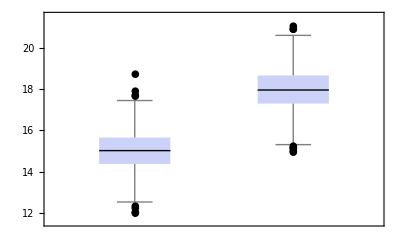

```mathematica
BoxWhiskerChart[dataNormDist, {{"MedianMarker",1},{"Outliers"}}]
```

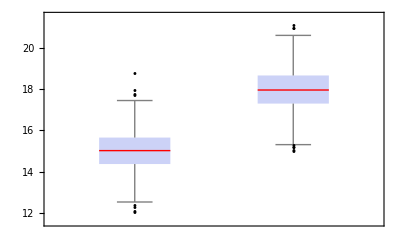

```mathematica
BoxWhiskerChart[dataNormDist, {"Outliers",{"MedianMarker",1, Directive[Thick, Red]}}]
```

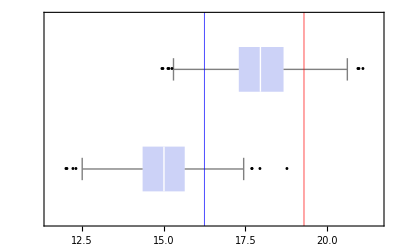

```mathematica
BoxWhiskerChart[dataNormDist,{"Outliers",{"MedianMarker",1,Directive[Thick,White]}},GridLines->{{{Quantile[Transpose@dataNormDist,.90][[1]],Blue},{Quantile[Transpose@dataNormDist,.90][[2]],Red}},None}, BarOrigin-> Left]
```

```mathematica
dataNormDist
```

(14.3213 | 14.4016 | 15.7758 | 15.8397 | 14.404 | 14.345 | 16.5277 | 15.2107 | 13.5973 | 15.8586 | 15.7076 | 13.7925 | 14.1447 | 15.1029 | 14.6095 | 12.8105 | 15.1167 | 13.9481 | 14.4184 | 15.7251 | 14.8838 | 15.2095 | 14.4592 | 14.8757 | 14.8511 | 15.7182 | 13.8792 | 14.286 | 14.7722 | 13.4612 | 15.6549 | 15.3255 | 13.3652 | 14.7625 | 15.3898 | 13.0575 | 15.6903 | 14.6559 | 14.4366 | 15.2189 | 14.9768 | 15.4034 | 15.079 | 15.2675 | 15.4029 | 13.3245 | 13.4203 | 14.6427 | 16.8084 | 16.2537 | 15.7312 | 14.1363 | 14.2463 | 15.4051 | 16.0134 | 15.3932 | 15.1376 | 15.6817 | 16.2556 | 16.0099 | 14.3991 | 14.6719 | 15.9309 | 14.5882 | 15.5377 | 13.2563 | 14.7507 | 16.406 | 15.1407 | 15.4985 | 14.0695 | 14.9974 | 16.7475 | 14.8263 | 15.7359 | 14.9162 | 15.1416 | 14.6119 | 14.0146 | 15.4843 | 15.0085 | 17.0635 | 14.6909 | 15.1719 | 16.1589 | 16.4721 | 14.1962 | 14.7406 | 12.2127 | 14.1497 | 15.0493 | 15.5439 | 13.4956 | 15.1368 | 15.1916 | 16.3705 | 16.3386 | 15.2668 | 18.7444 | 13.2379 | 15.085 | 13.4668 | 15.3808 | 14.7183 | 13.9504 | 14.5333 | 15.6189 | 14.9295 | 14.7979 | 13.0769 | 16.1979 | 16.0453 | 15.9266 | 15.8808 | 15.071 | 14.9278 | 15.8576 | 14.3643 | 15.9989 | 14.6922 | 15.2616 | 14.5491 | 13.4278 | 15.9283 | 15.4497 | 15.8532 | 14.0023 | 15.2433 | 13.734 | 14.1342 | 13.238 | 15.4948 | 14.8625 | 14.8638 | 15.2832 | 16.1273 | 13.908 | 14.9676 | 14.4501 | 14.879 | 14.3072 | 14.0237 | 14.554 | 14.2695 | 14.5189 | 16.3719 | 15.2464 | 13.755 | 15.3299 | 16.8456 | 15.849 | 16.9251 | 13.3689 | 14.7133 | 16.7305 | 14.595 | 14.9091 | 14.2468 | 13.8109 | 16.0671 | 16.1836 | 14.7277 | 15.943 | 14.1901 | 15.9273 | 14.1543 | 14.5418 | 15.1089 | 15.254 | 15.6059 | 14.5047 | 14.8648 | 16.5345 | 14.1139 | 16.8829 | 16.295 | 14.0631 | 14.8057 | 15.6605 | 15.2661 | 15.6018 | 15.2643 | 14.5015 | 17.136 | 16.9029 | 15.6271 | 15.4145 | 17.9247 | 15.8301 | 15.9571 | 14.4664 | 15.5588 | 14.2944 | 13.7561 | 15.2303 | 14.6579 | 15.7532 | 15.7202 | 15.1137 | 14.616 | 14.8782 | 14.0034 | 14.6498 | 16.3384 | 13.9962 | 15.3782 | 14.0739 | 14.999 | 16.628 | 14.0913 | 13.4065 | 14.2167 | 12.0088 | 15.5817 | 14.8686 | 15.0007 | 16.7406 | 15.1576 | 14.3635 | 15.3908 | 16.1755 | 15.6675 | 14.0375 | 14.7743 | 14.017 | 15.2937 | 16.725 | 15.3655 | 13.3381 | 14.5176 | 16.1883 | 15.0707 | 15.7079 | 13.5673 | 15.9115 | 15.967 | 14.0572 | 15.2718 | 14.029 | 14.998 | 15.997 | 15.3702 | 16.0294 | 15.8143 | 14.1671 | 15.0308 | 15.18 | 14.2485 | 14.2568 | 14.3302 | 14.421 | 15.262 | 14.243 | 14.0847 | 15.1223 | 14.9099 | 12.9869 | 15.3313 | 16.2144 | 15.6568 | 13.7866 | 13.9262 | 16.0978 | 16.3751 | 15.1698 | 13.8899 | 15.5991 | 13.5898 | 14.2246 | 15.053 | 14.4367 | 12.9793 | 14.6488 | 16.3135 | 15.1787 | 15.6392 | 16.618 | 14.2799 | 15.6669 | 15.3164 | 14.7631 | 15.3149 | 14.673 | 14.4317 | 17.2182 | 16.7573 | 15.7271 | 15.1265 | 17.0039 | 15.8438 | 15.0642 | 14.8097 | 15.9285 | 13.9024 | 14.4034 | 15.7247 | 14.6737 | 15.3433 | 14.9995 | 14.7081 | 16.1141 | 15.0141 | 15.0244 | 15.2767 | 15.7815 | 14.4872 | 15.0151 | 16.8706 | 15.5698 | 14.0343 | 13.8744 | 15.859 | 15.691 | 16.3743 | 14.1025 | 15.8028 | 15.6096 | 15.7669 | 15.8557 | 15.3184 | 15.0692 | 15.1753 | 14.4019 | 14.7824 | 14.4955 | 13.5872 | 15.8166 | 15.1614 | 15.1154 | 14.1184 | 13.6052 | 14.4224 | 15.5533 | 14.9341 | 15.1128 | 14.3069 | 15.2558 | 14.2168 | 16.9784 | 13.9727 | 14.5317 | 14.9577 | 14.4043 | 15.2335 | 14.163 | 15.8247 | 16.1287 | 14.8618 | 13.2063 | 16.995 | 14.6318 | 14.8019 | 15.4022 | 14.7175 | 14.7827 | 14.406 | 14.1486 | 15.102 | 15.1993 | 15.2936 | 15.1131 | 15.2791 | 15.7512 | 13.9147 | 16.9447 | 14.6791 | 15.1477 | 15.6619 | 16.0167 | 13.9523 | 16.128 | 14.3412 | 16.3696 | 17.6913 | 15.9869 | 15.5558 | 15.0138 | 15.5151 | 13.9235 | 15.0374 | 15.4607 | 14.6684 | 15.3275 | 15.8252 | 15.9387 | 15.5291 | 13.8854 | 15.1676 | 15.2915 | 14.675 | 15.4382 | 14.5136 | 16.5301 | 15.5908 | 14.5638 | 14.1655 | 15.0122 | 16.4383 | 15.0965 | 15.5801 | 14.2093 | 16.0167 | 13.8074 | 15.3349 | 13.4739 | 14.9159 | 14.7918 | 15.3535 | 12.856 | 15.0763 | 15.239 | 15.6243 | 16.5379 | 14.2739 | 14.2334 | 14.2918 | 15.0115 | 15.6253 | 14.9433 | 14.0134 | 14.6675 | 13.9229 | 14.8079 | 14.4554 | 14.153 | 15.4877 | 16.8063 | 15.8661 | 15.6277 | 12.9596 | 14.3132 | 17.0107 | 13.9726 | 14.4534 | 15.5089 | 14.368 | 15.1132 | 14.7665 | 14.8712 | 14.7571 | 13.9846 | 14.7918 | 14.853 | 14.1388 | 14.0229 | 13.1891 | 15.4168 | 14.6435 | 15.6101 | 13.9803 | 14.4516 | 15.246 | 15.4529 | 15.4199 | 14.3523 | 14.7792 | 15.7236 | 14.4488 | 13.5629 | 16.1485 | 15.0336 | 15.2441 | 15.3261 | 15.0355 | 14.7096 | 14.4589 | 15.452 | 16.9462 | 14.6744 | 15.2485 | 15.2346 | 17.0029 | 15.735 | 15.468 | 15.4766 | 14.3241 | 14.7562 | 15.6721 | 17.2102 | 14.9696 | 16.4611 | 14.7236 | 16.1382 | 14.8024 | 14.7744 | 13.8164 | 13.4987 | 13.1369 | 15.3554 | 13.1812 | 15.64 | 15.8191 | 16.2267 | 14.432 | 12.9308 | 14.1765 | 14.1164 | 15.7517 | 15.3359 | 13.8414 | 14.3278 | 14.7918 | 16.9089 | 16.9626 | 15.2733 | 14.9341 | 14.5048 | 13.04 | 15.2793 | 14.98 | 14.425 | 14.0611 | 14.0769 | 14.8252 | 14.2918 | 14.4634 | 15.3443 | 15.9547 | 15.9735 | 16.7924 | 16.1831 | 16.0832 | 15.8408 | 15.5691 | 15.1379 | 14.2486 | 15.4294 | 14.2402 | 14.4162 | 14.0437 | 14.9386 | 14.2567 | 15.2237 | 15.2568 | 16.1137 | 15.5822 | 15.4329 | 14.497 | 16.3436 | 14.7141 | 13.852 | 15.3528 | 16.3367 | 15.0328 | 16.3902 | 14.4818 | 14.9259 | 17.4443 | 15.0027 | 16.2875 | 16.0374 | 15.9409 | 15.5049 | 14.1226 | 14.5177 | 13.5121 | 13.4852 | 17.0021 | 14.843 | 15.764 | 15.3186 | 16.7887 | 14.7812 | 14.716 | 14.1436 | 16.2681 | 13.7296 | 15.5379 | 15.5446 | 14.8314 | 15.2754 | 15.9955 | 15.5468 | 13.6955 | 15.6344 | 17.0435 | 14.2085 | 15.7117 | 14.0959 | 13.2553 | 13.9289 | 12.6952 | 15.1115 | 14.558 | 15.4499 | 16.2579 | 15.75 | 14.6084 | 13.7409 | 15.6832 | 14.5532 | 15.886 | 13.1417 | 14.2766 | 14.2948 | 16.7024 | 14.1935 | 15.8343 | 14.0081 | 15.2654 | 15.7347 | 14.683 | 15.3645 | 16.0264 | 13.3695 | 15.1768 | 13.921 | 16.3194 | 15.6757 | 15.7985 | 16.2137 | 15.3229 | 16.0877 | 14.8621 | 15.8017 | 15.3216 | 13.8649 | 14.8548 | 15.5354 | 14.3867 | 14.6548 | 14.2205 | 16.3911 | 15.5827 | 15.3796 | 12.7785 | 15.6503 | 14.7768 | 14.1506 | 14.9302 | 15.7056 | 13.8895 | 14.1906 | 15.1686 | 14.9595 | 15.7319 | 14.3295 | 16.2081 | 16.4273 | 13.8722 | 12.5214 | 14.5895 | 13.5929 | 14.0496 | 15.1882 | 15.1856 | 14.1609 | 14.8775 | 14.4663 | 15.4224 | 12.8016 | 14.5864 | 16.2442 | 14.5346 | 14.3222 | 14.663 | 12.8386 | 14.9615 | 13.7082 | 14.647 | 15.093 | 15.2893 | 14.9074 | 13.7055 | 16.5858 | 16.3275 | 17.3125 | 16.5623 | 14.4671 | 14.7788 | 15.6751 | 13.5814 | 15.5906 | 15.0808 | 15.608 | 15.1174 | 13.5746 | 15.0328 | 16.9417 | 14.6594 | 14.5223 | 16.4752 | 15.9629 | 15.0388 | 16.3241 | 15.6951 | 15.5077 | 17.1222 | 15.7945 | 15.8046 | 16.1288 | 14.7743 | 14.4525 | 13.9066 | 14.9276 | 16.7556 | 14.8424 | 14.4235 | 15.1669 | 14.3255 | 16.9567 | 15.8256 | 14.0787 | 17.3106 | 15.1875 | 14.1579 | 13.4601 | 14.9778 | 13.7404 | 15.1526 | 13.7926 | 14.1951 | 15.8606 | 15.0318 | 13.9276 | 15.3483 | 15.3955 | 15.6189 | 15.4038 | 15.1649 | 15.7283 | 14.9655 | 14.8734 | 15.9448 | 15.2175 | 15.6472 | 14.8111 | 16.4318 | 15.0757 | 16.5156 | 13.6525 | 16.5929 | 16.1395 | 16.6901 | 14.5873 | 15.6473 | 13.2579 | 15.3183 | 16.5907 | 15.0706 | 14.6465 | 15.1392 | 13.9876 | 14.9759 | 15.1178 | 16.3259 | 14.8263 | 17.2237 | 14.9055 | 15.4664 | 15.7159 | 16.4798 | 13.6659 | 14.4693 | 15.0371 | 15.1333 | 16.0184 | 14.017 | 14.0153 | 14.4136 | 14.6797 | 14.016 | 13.3128 | 15.2103 | 15.2411 | 15.7986 | 14.4766 | 14.4032 | 14.3848 | 15.0401 | 15.6681 | 15.7952 | 15.3651 | 14.8416 | 16.2444 | 12.8837 | 14.9965 | 14.3628 | 14.2622 | 14.32 | 17.2417 | 14.7589 | 15.3275 | 15.7151 | 13.5182 | 15.1944 | 14.8653 | 15.4149 | 15.8873 | 13.6156 | 15.5554 | 15.9182 | 15.529 | 13.326 | 15.2192 | 15.0366 | 13.9766 | 14.9647 | 15.0585 | 15.2293 | 14.1213 | 15.5599 | 14.4709 | 14.2623 | 15.4175 | 16.6534 | 14.6688 | 16.1611 | 14.8098 | 14.2161 | 15.5353 | 14.5182 | 14.4541 | 15.9198 | 17.2818 | 14.0129 | 13.2016 | 13.1127 | 15.9063 | 15.4182 | 15.3356 | 14.2539 | 16.3378 | 13.7759 | 13.9739 | 15.1635 | 14.3768 | 14.4335 | 14.6593 | 14.8507 | 14.8706 | 14.7393 | 14.6717 | 15.9181 | 15.1834 | 15.0925 | 13.3055 | 13.7868 | 15.2772 | 13.7553 | 14.5401 | 15.0107 | 14.3284 | 16.176 | 14.4602 | 15.5998 | 14.8736 | 14.8937 | 15.435 | 14.5941 | 15.5346 | 15.3877 | 13.4457 | 15.1819 | 14.5803 | 16.1588 | 15.7498 | 15.4862 | 14.4216 | 16.5697 | 14.7098 | 14.4065 | 15.4636 | 14.4843 | 13.8932 | 14.9307 | 14.8858 | 16.0189 | 15.6713 | 13.8308 | 15.1015 | 15.4232 | 13.73 | 13.4166 | 15.44 | 13.58 | 15.8732 | 17.2219 | 14.9216 | 15.3569 | 13.7026 | 14.7873 | 15.2667 | 14.5018 | 13.9049 | 13.9017 | 14.3633 | 16.326 | 14.676 | 13.8805 | 14.5592 | 15.5016 | 15.5093 | 15.3966 | 15.0231 | 14.8449 | 15.6606 | 16.2045 | 13.0991 | 15.0806 | 14.6852 | 15.1053 | 14.4891 | 16.5139 | 13.4052 | 15.7833 | 13.5351 | 13.5018 | 16.0967 | 15.2038 | 17.6673 | 14.055 | 14.797 | 15.002 | 14.2943 | 16.5241 | 13.865 | 15.3289 | 15.2764 | 14.226 | 16.1474 | 14.6074 | 12.8626 | 14.0258 | 15.9585 | 13.4185 | 15.322 | 15.8771 | 15.8762 | 15.3348 | 13.9594 | 15.4017 | 16.2295 | 16.0707 | 15.5151 | 16.686 | 14.5574 | 17.2004 | 14.772 | 14.6378 | 14.6694 | 15.9454 | 16.0608 | 14.884 | 14.6785 | 16.4305 | 13.9741 | 17.1087 | 16.7753 | 13.3552 | 14.5717 | 14.1551 | 13.9898 | 15.342 | 14.353 | 13.765 | 14.8817 | 15.3873 | 15.2702 | 13.4805 | 13.8136 | 14.6326 | 14.4133 | 14.8441 | 13.1482 | 14.0752 | 15.3645 | 13.0441 | 12.3144 | 14.7746 | 14.86 | 14.9887 | 12.9037 | 14.4294 | 14.9536 | 15.1373 | 16.1845 | 14.5876 | 16.115 | 14.4827 | 16.4504 | 15.1211 | 14.2376 | 15.3954 | 14.7577 | 15.2556 | 13.5528 | 15.1519 | 14.4634 | 15.9203 | 13.9862 | 12.052 | 13.6777 | 14.4483 | 14.9428 | 15.0455 | 14.7774 | 16.5718 | 13.4755 | 13.3337
17.989 | 17.4913 | 16.7518 | 18.5588 | 17.7255 | 18.304 | 19.4616 | 17.7707 | 16.6244 | 19.3152 | 18.3221 | 18.5321 | 18.2385 | 18.5929 | 18.4194 | 16.9161 | 16.663 | 16.4956 | 18.4929 | 17.374 | 18.3087 | 18.1622 | 19.2161 | 17.0827 | 18.0344 | 17.7991 | 18.2246 | 19.3709 | 17.6488 | 18.2431 | 17.0996 | 17.2722 | 18.6256 | 18.6632 | 18.209 | 17.9739 | 18.5869 | 16.3422 | 18.7461 | 18.8306 | 18.868 | 16.7537 | 16.6161 | 17.4926 | 15.3098 | 17.5466 | 17.9744 | 20.0024 | 17.8701 | 18.8512 | 17.7157 | 20.6054 | 16.922 | 18.1975 | 17.5022 | 18.2603 | 19.0413 | 18.4521 | 18.2665 | 19.5764 | 19.0389 | 18.9048 | 17.0501 | 18.4035 | 17.9719 | 19.247 | 18.209 | 18.6139 | 18.7149 | 18.5736 | 18.8672 | 16.9432 | 15.9646 | 17.4211 | 18.8479 | 19.309 | 18.1249 | 17.6938 | 15.3047 | 16.7636 | 17.3971 | 17.3166 | 19.3477 | 18.7113 | 18.3488 | 18.8171 | 16.6236 | 15.9167 | 18.935 | 18.2175 | 18.3987 | 19.1616 | 15.1334 | 17.4805 | 16.9292 | 18.4637 | 18.96 | 19.995 | 17.6602 | 19.7877 | 19.5936 | 18.5954 | 18.1362 | 16.8971 | 18.4423 | 18.8338 | 17.7205 | 19.9911 | 17.982 | 18.006 | 18.9564 | 17.5059 | 18.4629 | 19.445 | 20.2491 | 15.6016 | 17.2198 | 16.9258 | 17.0083 | 16.6919 | 18.6197 | 17.7532 | 18.397 | 17.9565 | 18.4897 | 18.0457 | 17.7444 | 19.5443 | 18.7911 | 18.0467 | 17.2827 | 20.934 | 15.8508 | 17.704 | 16.6299 | 18.5599 | 17.3043 | 18.8493 | 15.9577 | 18.9799 | 15.9962 | 17.2306 | 17.0657 | 18.3661 | 20.1649 | 18.9457 | 17.8477 | 16.369 | 17.446 | 18.2048 | 16.9356 | 18.389 | 18.74 | 17.7692 | 15.6824 | 17.4439 | 19.6487 | 17.0053 | 17.6834 | 18.5314 | 18.6692 | 17.8958 | 18.2505 | 16.9054 | 18.9711 | 16.5125 | 16.7826 | 18.2792 | 18.4299 | 19.2407 | 19.7057 | 18.0168 | 18.4749 | 17.6087 | 18.0165 | 16.6322 | 18.7506 | 19.0844 | 18.4216 | 17.6849 | 15.903 | 16.0107 | 17.5752 | 18.374 | 17.2162 | 19.3826 | 18.652 | 16.8389 | 17.2166 | 17.076 | 16.8868 | 17.6477 | 16.5617 | 17.5691 | 19.2574 | 17.2288 | 17.7153 | 18.4315 | 17.7101 | 18.2319 | 18.4368 | 17.1353 | 17.0326 | 17.8953 | 18.0548 | 16.9733 | 18.6566 | 17.8638 | 17.8237 | 18.5749 | 17.5072 | 18.0974 | 14.9296 | 18.7208 | 20.4677 | 17.857 | 19.3915 | 17.4133 | 17.7699 | 16.9985 | 17.6407 | 17.2931 | 16.1285 | 17.3507 | 17.3406 | 16.0132 | 17.6501 | 18.5588 | 18.5276 | 16.5875 | 19.7264 | 18.6194 | 18.1171 | 17.4095 | 19.2792 | 18.9934 | 17.1501 | 17.4363 | 19.9508 | 15.9436 | 18.9929 | 18.8663 | 17.6255 | 19.2883 | 18.1197 | 18.4256 | 18.4706 | 17.3822 | 16.6871 | 17.6102 | 16.6712 | 19.9475 | 16.9791 | 16.6119 | 17.7809 | 18.6126 | 20.1111 | 18.4942 | 17.862 | 19.8882 | 18.5204 | 17.8162 | 17.6338 | 17.9805 | 18.8232 | 17.7423 | 17.9699 | 16.4203 | 15.4916 | 19.1033 | 19.5409 | 16.781 | 18.9224 | 17.6115 | 15.5117 | 19.9576 | 16.4031 | 19.1536 | 19.683 | 18.1059 | 17.5953 | 19.0037 | 16.6804 | 17.5298 | 17.9098 | 17.9469 | 19.0578 | 17.4468 | 19.2485 | 16.5151 | 17.9239 | 16.0492 | 17.3211 | 18.2365 | 16.4036 | 19.1815 | 17.1795 | 17.6554 | 19.1704 | 18.23 | 16.8482 | 17.7955 | 18.2074 | 17.6432 | 17.4181 | 17.975 | 16.9355 | 17.6937 | 17.5658 | 18.8818 | 17.081 | 17.6922 | 16.5357 | 17.8537 | 18.963 | 17.351 | 17.2257 | 17.0861 | 18.3183 | 17.4061 | 17.8467 | 16.81 | 17.2719 | 16.6752 | 19.4375 | 18.6277 | 20.0948 | 16.5082 | 17.6374 | 19.5997 | 17.9492 | 19.2902 | 16.3068 | 16.4873 | 19.2943 | 18.9947 | 18.9783 | 18.023 | 17.8579 | 17.5201 | 16.4281 | 18.0187 | 17.7007 | 18.7312 | 17.9778 | 19.469 | 16.8957 | 17.5955 | 19.2857 | 18.3292 | 17.3866 | 17.3697 | 16.3495 | 16.8879 | 18.5197 | 19.5737 | 18.2181 | 17.5934 | 18.4734 | 17.4762 | 21.0706 | 19.7147 | 18.5302 | 17.2084 | 17.3701 | 20.9239 | 16.9501 | 18.9708 | 15.6665 | 17.7784 | 17.7429 | 17.5967 | 17.8452 | 19.639 | 18.2361 | 17.6822 | 17.318 | 16.9222 | 17.2962 | 18.179 | 18.8901 | 19.007 | 17.3171 | 17.6049 | 18.841 | 17.8015 | 18.5782 | 19.1868 | 17.4404 | 15.232 | 17.0477 | 17.3939 | 19.7908 | 17.3392 | 18.5352 | 19.1961 | 19.3438 | 17.6676 | 17.4542 | 19.1787 | 17.9597 | 19.9287 | 19.4976 | 18.5412 | 20.1516 | 16.7984 | 17.7975 | 17.906 | 16.2103 | 19.261 | 18.5515 | 18.4907 | 16.1251 | 17.3365 | 17.5603 | 18.682 | 19.8301 | 16.5879 | 18.0763 | 18.4709 | 18.1122 | 17.2166 | 17.9617 | 19.6563 | 16.9887 | 17.1986 | 18.6213 | 16.4787 | 17.6304 | 19.8839 | 18.5749 | 18.3044 | 20.1372 | 18.7164 | 18.6846 | 18.9609 | 18.0246 | 17.7268 | 15.9998 | 18.2103 | 16.4446 | 18.3256 | 17.5344 | 17.4618 | 17.4626 | 17.8693 | 18.4011 | 17.5188 | 16.3316 | 17.4243 | 20.3403 | 19.6322 | 17.4807 | 16.6767 | 18.9275 | 17.4294 | 18.9308 | 18.7198 | 17.5383 | 18.5876 | 19.3475 | 18.0346 | 17.1581 | 18.641 | 17.5779 | 17.2457 | 16.0245 | 17.2094 | 17.8231 | 17.2537 | 17.8444 | 18.5607 | 17.1131 | 17.9669 | 18.5282 | 18.4056 | 18.7135 | 16.685 | 17.9732 | 18.6327 | 18.1684 | 19.3151 | 20.1735 | 18.6034 | 19.6624 | 18.1341 | 17.1765 | 19.7191 | 17.8457 | 19.3129 | 18.1041 | 16.0713 | 17.9578 | 17.9864 | 18.9542 | 18.6809 | 19.7394 | 17.3293 | 16.9714 | 18.5328 | 18.841 | 17.3623 | 18.4818 | 17.6781 | 17.716 | 16.8511 | 17.544 | 17.3563 | 18.9004 | 20.1059 | 18.1753 | 16.6843 | 18.388 | 18.9635 | 18.869 | 18.6134 | 17.6683 | 17.9395 | 17.8177 | 19.0318 | 16.9103 | 16.9318 | 19.6002 | 19.1473 | 18.0069 | 17.8651 | 16.8931 | 18.472 | 17.8658 | 17.6231 | 17.1113 | 19.2837 | 16.4566 | 17.7977 | 17.2561 | 16.8672 | 17.6721 | 18.7224 | 17.4823 | 16.4771 | 16.6466 | 17.2888 | 17.2154 | 20.1545 | 17.2615 | 20.3068 | 18.3065 | 19.8078 | 19.5649 | 19.3522 | 17.9587 | 18.8773 | 19.0997 | 19.4377 | 17.6508 | 17.6431 | 17.4195 | 18.132 | 16.2761 | 17.8113 | 17.5813 | 18.2608 | 18.2329 | 17.8778 | 17.1364 | 17.618 | 17.2631 | 19.1366 | 17.4401 | 19.2832 | 16.5687 | 17.4006 | 17.1895 | 17.5286 | 18.7779 | 18.2267 | 18.5393 | 18.9837 | 19.1322 | 17.9058 | 18.0385 | 17.9651 | 18.1945 | 18.5036 | 18.1886 | 17.5292 | 18.8985 | 18.921 | 18.448 | 18.7624 | 17.1586 | 18.1266 | 17.2527 | 18.9482 | 18.7995 | 19.3703 | 17.721 | 17.6793 | 19.1431 | 17.2784 | 17.1069 | 18.1257 | 18.4363 | 17.0174 | 17.6244 | 17.1842 | 18.4611 | 17.4821 | 19.2982 | 18.6073 | 18.2315 | 18.104 | 18.0723 | 16.0853 | 17.9437 | 18.1939 | 17.8494 | 18.6605 | 17.7251 | 17.7916 | 18.4688 | 16.8567 | 18.4296 | 17.9519 | 18.8984 | 18.3785 | 17.4761 | 17.5037 | 17.5373 | 18.318 | 16.9963 | 17.2962 | 15.9479 | 17.7565 | 19.3714 | 17.6529 | 16.1798 | 18.1004 | 20.2602 | 17.6651 | 18.6785 | 17.6135 | 19.0607 | 17.8787 | 19.6028 | 16.5605 | 19.3613 | 17.5275 | 18.2197 | 17.8701 | 18.8185 | 15.9661 | 16.6221 | 15.8308 | 17.4057 | 17.2681 | 18.4388 | 17.0247 | 18.5467 | 18.015 | 17.9008 | 17.4873 | 19.3686 | 17.1225 | 16.9688 | 19.3985 | 18.7019 | 18.1999 | 17.8765 | 17.5228 | 16.1964 | 16.2068 | 18.288 | 16.4533 | 18.1499 | 19.2292 | 18.3563 | 18.8096 | 18.0676 | 17.7595 | 18.2172 | 18.7156 | 17.1934 | 20.1097 | 16.759 | 17.8809 | 19.2904 | 15.5369 | 19.2223 | 17.3242 | 16.6399 | 16.5072 | 16.7968 | 18.6296 | 18.0428 | 18.4363 | 18.9378 | 17.5927 | 16.9058 | 17.6095 | 17.9821 | 17.6112 | 16.6407 | 18.7909 | 17.9373 | 17.0246 | 16.9611 | 16.5715 | 18.0621 | 17.5729 | 19.1522 | 18.4023 | 17.5409 | 20.5204 | 18.2408 | 18.976 | 17.949 | 16.8839 | 17.2788 | 17.7591 | 17.9627 | 17.1386 | 18.3282 | 17.595 | 18.17 | 16.4708 | 17.9749 | 19.4207 | 19.6608 | 18.1846 | 18.6864 | 17.1589 | 19.2707 | 18.0523 | 18.3638 | 18.7514 | 17.0607 | 17.1123 | 18.4887 | 17.0165 | 17.1029 | 18.9077 | 18.1184 | 19.0283 | 19.9375 | 18.174 | 17.9767 | 18.6921 | 18.1873 | 17.6532 | 18.8097 | 19.416 | 19.3882 | 20.1772 | 18.5181 | 15.1549 | 17.952 | 18.7112 | 18.8091 | 19.2084 | 18.2951 | 18.5566 | 17.8561 | 16.9291 | 19.0293 | 17.6774 | 17.4864 | 18.0204 | 16.7092 | 17.8088 | 19.7648 | 19.0221 | 18.6448 | 16.7467 | 17.7918 | 18.2253 | 16.8711 | 18.2285 | 18.9882 | 19.2064 | 19.396 | 18.3022 | 17.9907 | 17.3785 | 19.6869 | 19.2027 | 17.6962 | 16.6219 | 17.0819 | 19.1759 | 18.5984 | 18.3098 | 16.9873 | 17.5402 | 17.9452 | 17.0286 | 18.1364 | 18.951 | 17.5736 | 17.8887 | 16.4111 | 16.8256 | 17.2894 | 16.7994 | 15.6926 | 17.4317 | 17.3149 | 17.7565 | 17.2685 | 17.8139 | 15.9947 | 17.7238 | 19.2049 | 17.5156 | 18.1473 | 19.2607 | 18.0798 | 19.0638 | 17.3852 | 18.8759 | 18.8396 | 19.6003 | 18.2754 | 18.1253 | 18.2153 | 18.6742 | 16.9308 | 17.2915 | 16.9994 | 17.4417 | 17.7005 | 17.8642 | 17.151 | 17.1119 | 16.1825 | 18.0225 | 16.4461 | 18.5853 | 17.3281 | 18.0366 | 17.6635 | 17.5949 | 17.696 | 18.559 | 18.5573 | 17.7234 | 16.5342 | 18.533 | 17.0474 | 15.4064 | 19.259 | 18.4389 | 16.1766 | 19.2076 | 17.5384 | 17.8309 | 18.2219 | 17.9449 | 17.9496 | 18.8474 | 17.6889 | 16.2246 | 18.66 | 17.258 | 19.2279 | 17.3081 | 17.6372 | 17.3609 | 19.715 | 18.7631 | 19.2835 | 18.5775 | 18.049 | 20.2065 | 18.7164 | 15.9857 | 20.0726 | 19.379 | 17.4903 | 18.3904 | 14.973 | 17.5525 | 17.3921 | 18.4063 | 16.2011 | 18.4537 | 17.7195 | 16.7802 | 18.6542 | 18.8246 | 16.6763 | 19.76 | 17.7026 | 17.7848 | 16.8651 | 18.7222 | 17.8559 | 18.3306 | 17.5021 | 19.1211 | 18.5103 | 18.0603 | 16.9926 | 17.4784 | 17.1665 | 15.7696 | 17.8564 | 17.3435 | 19.3314 | 17.0425 | 18.4173 | 16.0791 | 18.9135 | 18.3464 | 17.0031 | 17.4838 | 16.0034 | 19.1426 | 18.5071 | 19.19 | 18.1292 | 16.9389 | 16.4906 | 18.8636 | 17.4544 | 17.952 | 18.6329 | 17.9547 | 15.6862 | 17.1884 | 19.2208 | 16.9238 | 17.9339 | 19.0397 | 16.1854 | 18.1977 | 17.16 | 18.5697 | 17.9082 | 18.6155 | 18.4748 | 17.9769 | 17.0427 | 18.1063 | 17.5677 | 16.287 | 16.1184 | 18.9293 | 19.1059 | 17.76 | 17.1773 | 18.788 | 16.8453 | 18.1176 | 18.3993 | 19.5629 | 16.5164 | 16.9699 | 18.02 | 18.2448 | 17.9802 | 16.4229 | 17.6068 | 16.1479 | 16.9151 | 17.7359 | 18.3726 | 19.6103 | 17.5824 | 19.1455 | 18.1017 | 17.9225 | 18.1797 | 15.6529 | 18.7947 | 18.9245 | 17.6593 | 18.5355 | 17.712 | 17.7814 | 17.2202 | 17.8517 | 18.2539 | 18.1789 | 16.7928 | 18.9214 | 17.3867 | 19.6708 | 18.4281 | 18.1948 | 18.8177 | 18.0052 | 17.6156 | 16.5662 | 15.9879 | 17.1309 | 17.7753 | 19.2822 | 17.4343 | 17.0926)

```mathematica
Quantile[Transpose@dataNormDist,.90]
```

{16.2444,19.2835}

```mathematica
Quantile[Transpose@dataNormDist,.90][[1]]
```

16.2444

### Log Normal Distribution

```mathematica
Clear[μ]; μrange = {1,2,3};logNormDist = LogNormalDistribution[μ,1]
```

LogNormalDistribution[μ,1]

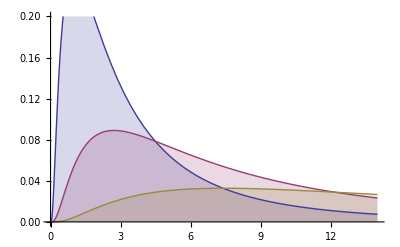

```mathematica
Plot[Evaluate@Table[PDF[logNormDist,x],{μ,μrange}], {x,0,14},Filling-> Axis,PlotRange->{0,0.2}]
```

```mathematica
dataLogNormDist = Evaluate@Table[RandomVariate[logNormDist,100], {μ,μrange}]
```

(3.62277 | 0.914549 | 11.2393 | 2.72551 | 6.00023 | 0.692511 | 17.7935 | 1.87774 | 0.635186 | 4.45727 | 30.1149 | 0.906456 | 10.4339 | 5.3998 | 0.139799 | 5.23092 | 7.13532 | 2.18691 | 2.00806 | 0.450047 | 3.11335 | 1.69757 | 2.80024 | 0.917415 | 1.90096 | 10.9624 | 4.01671 | 0.663688 | 1.90874 | 2.26045 | 1.60152 | 4.43538 | 0.401991 | 4.97453 | 6.77278 | 0.367955 | 1.28326 | 6.43088 | 2.15103 | 0.626827 | 4.42801 | 2.65172 | 2.30711 | 25.9904 | 2.51152 | 3.12099 | 2.62753 | 3.51864 | 1.70112 | 3.69778 | 0.902583 | 3.0063 | 9.81599 | 0.656175 | 0.8417 | 7.12048 | 1.20549 | 4.25642 | 1.29541 | 55.9676 | 0.782562 | 1.82972 | 5.67683 | 5.88529 | 5.33446 | 2.11566 | 7.04592 | 1.14158 | 0.322632 | 0.992236 | 3.50399 | 6.28242 | 2.34968 | 2.88031 | 13.1587 | 4.90922 | 5.89029 | 1.16049 | 0.356309 | 0.386922 | 6.81742 | 3.44465 | 16.6276 | 0.468215 | 0.113649 | 3.67605 | 2.40686 | 0.564327 | 2.44771 | 2.84022 | 18.4511 | 2.6472 | 0.493107 | 1.5722 | 1.14909 | 7.06001 | 16.3808 | 3.79094 | 2.31188 | 1.26327
19.7863 | 3.64388 | 2.80387 | 4.12298 | 4.46953 | 6.9043 | 3.53941 | 13.7318 | 28.4925 | 3.71876 | 7.05215 | 4.5429 | 9.89896 | 4.25111 | 4.23116 | 3.17712 | 39.8547 | 14.5429 | 11.2536 | 8.36286 | 4.07801 | 2.59198 | 24.9456 | 12.7983 | 15.9091 | 6.9214 | 2.55888 | 142.728 | 14.9628 | 39.0458 | 7.52435 | 2.29926 | 98.8545 | 4.67173 | 1.94742 | 23.3849 | 3.13576 | 6.74651 | 2.60295 | 33.6501 | 3.75158 | 22.0053 | 10.6937 | 9.9893 | 16.1658 | 52.7763 | 8.17633 | 29.479 | 9.4634 | 11.7894 | 7.82173 | 3.05156 | 33.3922 | 17.0019 | 115.75 | 19.1845 | 8.75768 | 10.3541 | 3.94034 | 21.2186 | 16.8248 | 15.8853 | 2.88848 | 0.736207 | 10.4669 | 9.04712 | 1.22411 | 6.37311 | 2.30318 | 7.32434 | 3.60892 | 65.3684 | 12.7434 | 3.85505 | 12.6382 | 5.5283 | 14.3194 | 7.59748 | 13.8269 | 1.07954 | 2.61105 | 8.56814 | 29.6238 | 33.9926 | 9.54274 | 15.6527 | 3.13399 | 5.96073 | 7.56686 | 0.985065 | 10.2994 | 94.7318 | 10.2271 | 11.5849 | 10.9269 | 49.1993 | 14.9523 | 15.0334 | 8.72036 | 49.3421
30.5549 | 10.8674 | 10.5713 | 20.0854 | 31.4282 | 3.62677 | 6.55779 | 12.581 | 28.5145 | 1.76397 | 4.78897 | 6.74922 | 88.7885 | 27.226 | 94.5501 | 46.217 | 6.35558 | 7.24297 | 32.5678 | 16.1625 | 33.9348 | 16.2296 | 12.3755 | 90.0995 | 25.6837 | 15.8937 | 59.4173 | 17.4756 | 2.56389 | 58.3445 | 33.6522 | 115.518 | 21.9407 | 113.033 | 159.484 | 6.75641 | 126.73 | 34.513 | 21.2641 | 11.6516 | 5.4259 | 61.5273 | 10.6309 | 25.1488 | 12.7863 | 18.9775 | 208.2 | 3.78139 | 14.1432 | 2.06676 | 15.8073 | 23.9039 | 4.864 | 43.5517 | 12.0591 | 2.99905 | 27.2394 | 21.923 | 12.9364 | 6.73923 | 10.7694 | 53.0846 | 29.7501 | 156.365 | 7.35004 | 10.704 | 9.21953 | 50.1726 | 91.994 | 6.98342 | 4.28811 | 3.57771 | 28.9949 | 36.8606 | 5.6317 | 6.51204 | 7.65566 | 57.0205 | 47.4628 | 16.106 | 7.94356 | 6.6941 | 9.3259 | 8.45912 | 4.69887 | 18.6575 | 20.265 | 29.5623 | 82.4668 | 29.0945 | 9.85683 | 82.584 | 37.6013 | 16.802 | 10.4283 | 2.97831 | 74.1919 | 86.8705 | 34.2272 | 46.9082)

```mathematica
PDF[LogNormalDistribution[μ,σ],x]
```

Piecewise[{{(E^(-(log(x)-μ)^2/(2 σ^2)))/(√(2 π) σ x), x>0}, {0, True}}]

```mathematica
f[4]
```

16

```mathematica
x//f
```

f(x)

```mathematica
x~f~y
```

f(x,y)

```mathematica
StringJoin["lrs","pqz"]
```

lrspqz

```mathematica
"lrs"~StringJoin~"pqz"~StringJoin~"abc"
```

lrspqzabc

```mathematica
x=2
```

2

```mathematica
f[x_]:=x^2
```

```mathematica
Quantile[LogNormalDistribution[μ,σ],1/2]
```

E^μ

```mathematica
Median[LogNormalDistribution[μ,σ]]
```

E^μ

```mathematica
StandardDeviation[LogNormalDistribution[μ,σ]]
```

√((E^(σ^2)-1) E^(2 μ+σ^2))

```mathematica
%4/.{μ->1,σ->1}
```

y^2

```mathematica
Mean[NormalDistribution[μ,σ]]
```

μ

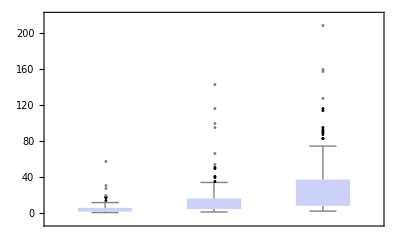

```mathematica
BoxWhiskerChart[dataLogNormDist, {{"MedianMarker"},{"Outliers"]
```